## 1 Efficient evaluation of convolutions

### 1)

```mathematica
ClearAll[l]
Θ=10;
ϵ=1/2^8;
l[X__]:=Table[X ,{θ,-Θ,Θ-ϵ ,2Θ ϵ}];
```

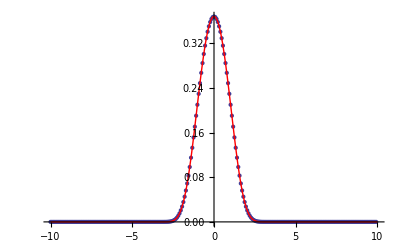

```mathematica
Show[{l[θ],l[ⅇ^(-Cosh[θ])]}//Transpose//ListPlot[#,PlotRange->All]&, Plot[ⅇ^(-Cosh[θ]),{θ,-10,10},PlotStyle->Red,PlotRange->All]]
```

### 2)

```mathematica
ClearAll[F]
F[+1][X_]:=Fourier[X];
F[-1][X_]:=RotateRight[2 Θ/√Length[X]InverseFourier[X],Length[X]/2];
```

Now lets test these tools on an example convolution 


f(θ)=∫_(-∞)^∞ ⅆϑ ⅇ^(- cosh(ϑ))/Cosh[θ-ϑ]

First use NIntegrate

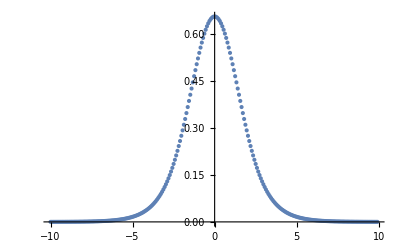
{1.50502,-Graphics-}

```mathematica
Dynamic[θ//N]
l[{θ,NIntegrate[ⅇ^(-Cosh[ϑ])/Cosh[θ-ϑ],{ϑ,-Θ,Θ}]}]//Quiet//ListPlot//Timing
```

Now use Fourier

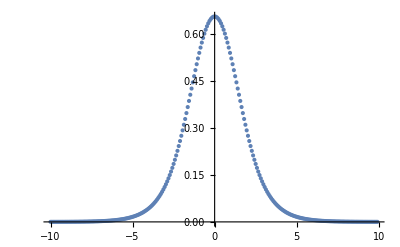
{0.027933,-Graphics-}

```mathematica
{l[θ],F[-1][F[+1][l[1/Cosh[θ]]]F[+1][l[ⅇ^(-Cosh[θ])]]]}//Transpose//ListPlot//Timing
```

: )

```mathematica
1.654/0.015
```

110.267

## 2 TBA: solution by interation

### 1)

```mathematica
Table[𝒦[a,b][θ_]=1/(2π ⅈ) D[Log[Product[Sinh[θ/2+ⅈ (π (p-1))/(2 4)]/Sinh[θ/2-ⅈ (π (p-1))/(2 4)] Sinh[θ/2+ⅈ (π (p+1))/(2 4)]/Sinh[θ/2-ⅈ (π (p+1))/(2 4)],{p,Abs[a-b]+1,a+b-1,2}]], θ]//FullSimplify,{a,1,4-1},{b,1,4-1}];
```

```mathematica
Table[𝒦[a,b][θ],{a,1,4-1},{b,1,4-1}]//MatrixForm
```

(-Sech[θ]/(2 π) | -(√2 Cosh[θ] Sech[2 θ])/π | -Sech[θ]/(2 π)
-(√2 Cosh[θ] Sech[2 θ])/π | -Sech[θ]/π | -(√2 Cosh[θ] Sech[2 θ])/π
-Sech[θ]/(2 π) | -(√2 Cosh[θ] Sech[2 θ])/π | -Sech[θ]/(2 π))

### 2)

We replace the Y-functions with constants as θ→-∞.  Now we can perform the integrals on the RHS by just integrating the kernels.  This gives

```mathematica
(M=(Table[𝒦[a,b][θ],{a,1,4-1},{b,1,4-1}]//FullSimplify//NIntegrate[#,{θ,-∞,∞}]&//Rationalize[#,10^-9]&))//MatrixForm
```

(-1/2 | -1 | -1/2
-1 | -1 | -1
-1/2 | -1 | -1/2)

Now solve the resulting algebraic equations for the constants

```mathematica
c=((y/@Range[1,3])/.((Log[#]+M.Log[1+1/#])&@(y/@Range[1,3])==0//Solve[#,(y/@Range[1,3])]&//Flatten))
```

{2,3,2}

### 3)

Now we compute  K_ab(θ-ϑ)*cut(ϑ)log(1+1/c_b)

```mathematica
Dynamic[{a,b,θ}//N]
Table[C∞[a]=Sum[l[NIntegrate[𝒦[a,b][ϑ-θ] 1/2(1+Tanh[-ϑ])Log[1+1/c⟦b⟧],{ϑ,-∞,+∞}]],{b,1,4-1}],{a,1,4-1}]//Quiet;
```

### 4)

Now we will implement the recursive procedure for solving the TBA.

First implement the kernels using the Fourier commands from section 1.

```mathematica
ClearAll[K]
Table[k[a,b]=F[+1][l[𝒦[a,b][θ]]],{a,1,4-1},{b,1,4-1}];
K[a_,b_][f_]:=F[-1][k[a,b] F[+1][f]];
```

Now the TBA input and the recursion

```mathematica
ClearAll[Y]
R=√(2 π) Gamma[5/4]/Gamma[7/4];
m[a_]=Sin[π a/4]/Sin[π/4];
Y[a_][0]=l[ⅇ^(m[a] R ⅇ^θ)];
cut =l[1/2(1+Tanh[-θ])];

Y[a_][n_]:=Y[a][n]=Y[a][0] ⅇ^(-C∞[a]-Sum[K[a,b][Log[1+1/Y[b][n-1]]-cut Log[1+1/c⟦b⟧]],{b,1,4-1}]);
```

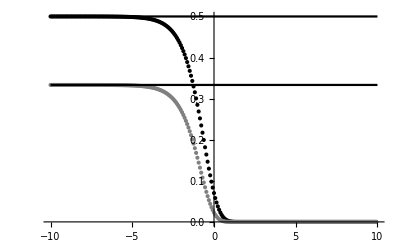

```mathematica
plt=Show[{l[θ],1/Y[1][20]}//Transpose//ListPlot[#,PlotStyle->Black]&,{l[θ],1/Y[2][20]}//Transpose//ListPlot[#,PlotStyle->Gray]&,Plot[{1/2,1/3},{θ,-Θ,Θ},PlotStyle->Black],PlotRange->All]
```

## Evaluating spectrum

It is useful to make an interpolation of the final Y-function as follows:

```mathematica
ClearAll[Υ]
Table[yint[a]=Interpolation[{l[θ],1/Y[a][20]}//Transpose],{a,1,4-1}];
Υ[a_][ϑ_]:= Which[ϑ≤-Θ,1/c⟦a⟧,ϑ≥Θ,ⅇ^(-m[a] R ⅇ^ϑ),-Θ<ϑ<Θ,yint[a][ϑ]];
```

I define the function Υ so that integrations can be now be done over the full real line.

### 1)

Solving the Y-system you should find

Y_1(θ+ⅈ 3π/4)=(1+((1+Y_1(θ+ⅈ π/4))(1+Y_3(θ+ⅈ π/4)))/(Y_2(θ)))/(Y_1(θ+ⅈ π/4))

### 2)

As we continue γ up to π/4 the poles of the kernel move upward, thus the pole will be just below the real axis when γ→π/4.  Thus we should add the half residue with a minus sign

```mathematica
Res[θ_]=-1/2 2 π ⅈ Residue[Cosh[-θ-ⅈ π/4+ϑ]/Cosh[2(-θ-ⅈ π/4+ϑ)] ⅇ^(-Cosh[ϑ]),{ϑ,θ}];
```

Now define the integral using the PrincipalValue and adding the half reside

```mathematica
ClearAll[fPV]
fPV[θ_][ⅈ π/4]:=Res[θ]+NIntegrate[Cosh[-θ-ⅈ π/4+ϑ]/Cosh[2(-θ-ⅈ π/4+ϑ)] ⅇ^(-Cosh[ϑ]),{ϑ,-∞,θ,∞},"Method"->{"PrincipalValue"}]
```

```mathematica
fPV[0.1][ⅈ π/4]
```

0.638185-0.0296788 ⅈ

We can compare with the value obtained from an ⅈ ε prescription

```mathematica
ClearAll[f]
f[ε_][θ_][ⅈ π/4]:=NIntegrate[Cosh[-θ-ⅈ π/4+ⅈ ε+ϑ]/Cosh[2(-θ-ⅈ π/4+ⅈ ε+ϑ)] ⅇ^(-Cosh[ϑ]),{ϑ,-∞,θ,∞},"Method"->{"PrincipalValue"}]
```

```mathematica
f[0.0001][0.1][ⅈ π/4]
```

0.638155-0.0296736 ⅈ

### 3)

Now we compute the Y-functions Y_1(θ+ⅈ π/4) and Y_3(θ+ⅈ π/4).

The half residues are given by

```mathematica
ClearAll[R12,R32]
R12[θ_]:=R12[θ]=-1/2Log[1+Υ[2][θ]]
R32[θ_]:=R32[θ]=-1/2Log[1+Υ[2][θ]]
```

Putting θ→θ+ⅈ γ in the TBA and continueing to γ=π/4 gives

```mathematica
ClearAll[y]
y[1][θ_][ⅈ π/4]:=y[1][θ][ⅈ π/4]=ⅇ^(R m[1] ⅇ^(θ+ⅈ π/4))ⅇ^(-R12[θ]-NIntegrate[Sum[𝒦[1,b][θ+ⅈ π/4-ϑ]Log[1+Υ[b][ϑ]],{b,1,4-1}],{ϑ,-Θ,θ,Θ},"Method"->{"PrincipalValue"}]-NIntegrate[Sum[𝒦[1,b][θ+ⅈ π/4-ϑ]Log[1+1/c⟦b⟧],{b,1,4-1}],{ϑ,-∞,θ,-Θ},"Method"->{"PrincipalValue"}])
y[3][θ_][ⅈ π/4]:=y[3][θ][ⅈ π/4]=ⅇ^(R m[3] ⅇ^(θ+ⅈ π/4))ⅇ^(-R32[θ]-NIntegrate[Sum[𝒦[3,b][θ+ⅈ π/4-ϑ]Log[1+Υ[b][ϑ]],{b,1,4-1}],{ϑ,-Θ,θ,Θ},"Method"->{"PrincipalValue"}]-NIntegrate[Sum[𝒦[3,b][θ+ⅈ π/4-ϑ]Log[1+1/c⟦b⟧],{b,1,4-1}],{ϑ,-∞,θ,-Θ},"Method"->{"PrincipalValue"}])
```

```mathematica
{y[1][0.1][ⅈ π/4],y[3][0.1][ⅈ π/4]}
```

{-1.95731+7.72487 ⅈ,-1.95731+7.72487 ⅈ}

### 4)

Make an interpolation of Y_1(θ+ⅈ 3π/4).  Recall that Y_1=Y_3.

```mathematica
Dynamic[θ//N]
det=Table[{θ,(1+((1+y[1][θ][ⅈ π/4])^2(*(1+y[3][θ][ⅈ π/4])*))/(1/Υ[2][θ]))/(y[1][θ][ⅈ π/4])},{θ,0,2,1/10}]//Chop//Interpolation//Quiet
```

InterpolatingFunction[{{0., 2.}}, <>]

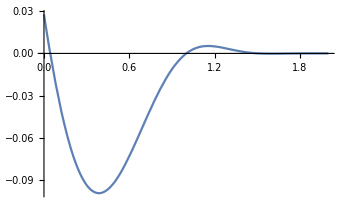

```mathematica
DetPlot=(det[θ]//Plot[#//Re,{θ,0,2}]&)
```

```mathematica
(θ/.(Table[FindRoot[Re[det[θ]]==0,{θ,θ0}],{θ0,0,1.5,1/10}]//Quiet))//Rationalize[#,10^-9]&//Union//N//Exp[4/3#]&
```

{1.06023,3.79977,7.45754,11.723}

Now lets compare the zeros with the known eigenvalues of the anharmonic oscillator:

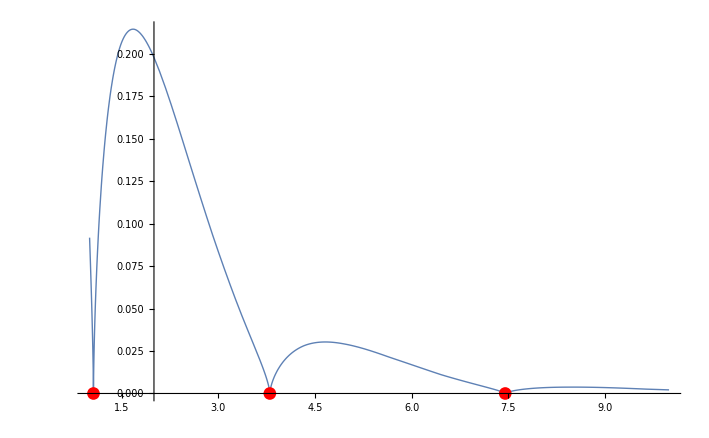

```mathematica
DetPlot2=(Abs[Re[det[3/4Log[Ε]]]]^(1/1.5)//Plot[#//Re,{Ε,1,10},PlotPoints->100,PlotStyle->Thick]&);
DoreyTateoEigenvalues ={{1.06036209048418,3.79967302980139,7.455693798672,11.64474551137815 },Table[0,{4}]}//Transpose//ListPlot[#,PlotStyle->Red]&;
Show[DetPlot2,DoreyTateoEigenvalues]
```

So we can see the eigenvalues computed by the two methods agree quite well.  Most of the error is probably due to the interpolations made in the last few steps, which loses the exponential precision of the spectral method we have been using (Fourier).  One could redo the last part of the exercise using Fourier to check  (this would also be much faster...).